```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
l=Flatten @ Import["test2-carry.dat"];
```

```mathematica
len=Length[l]
1./Sqrt[len]
```

65536

0.00390625

```mathematica
Mean[l]
StandardDeviation[l]
```

-0.000935098

1.04024

{1.,0.696516,0.589346,0.539636,0.498472,0.468731,0.441205,0.42126,0.401801,0.386075,0.371163,0.357122,0.348036,0.338123,0.326295,0.319076,0.308872,0.302907,0.297319,0.290788,0.284325}

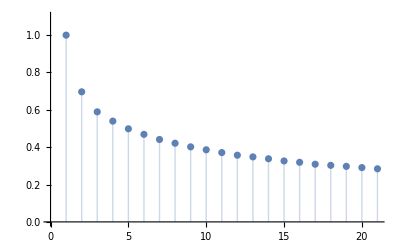

8.98707

```mathematica
cf=CorrelationFunction[l,{20}]
ListPlot[cf,Filling->0,PlotRange->{0,1.1}]
Total[cf]
```

```mathematica
(* Allan variance estimate *)
diffs=Most[l]-Rest[l];
sqdiffs=diffs^2;
sumsqdiffs=Total[sqdiffs];
avar=sumsqdiffs/(2len)
adev=Sqrt[avar]
```

0.328384

0.573048

```mathematica
(* Convert to integers *)
lint=N@Round[l];
Mean[lint]
StandardDeviation[lint]
```

0.

1.08048

```mathematica
(* Allan variance estimate *)
diffs=Most[lint]-Rest[lint];
sqdiffs=diffs^2;
sumsqdiffs=Total[sqdiffs];
avar=sumsqdiffs/(2len)
adev=Sqrt[avar]
```

0.49575

0.704095

{1.,0.575339,0.547368,0.50166,0.462514,0.43551,0.409173,0.39256,0.372876,0.358943,0.346513,0.332109,0.323339,0.313653,0.302347,0.296596,0.286885,0.279827,0.274821,0.267606,0.261907}

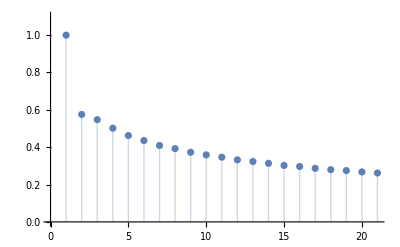

8.34155

```mathematica
cf=CorrelationFunction[N[lint],{20}]
ListPlot[cf,Filling->0,PlotRange->{0,1.1}]
Total[cf]
```

0.

{a→23915.2,x0→-0.00555375,σ→1.09862}

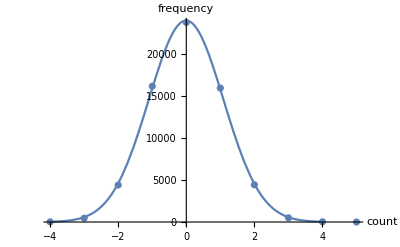

```mathematica
(* Distribution *)
ta=Tally[lint];
x0est=Sort[ta,#1[[2]]>#2[[2]]&][[1,1]]
p1=ListPlot[ta,AxesLabel->{"count","frequency"},LabelStyle->Larger];
fnc=a Exp[-(x-x0)^2/(2σ^2)];
sol=FindFit[ta,fnc,{{a,20000},{x0,x0est},{σ,1}},x]
fnc=fnc/.sol;
p2=Plot[fnc,{x,-4,4},PlotRange->All];
pp=Show[p1,p2]
```

1.00013

{1.,0.0412189,0.0067496,0.0060904,0.00185927,0.00756443,-0.000174394,0.00653818,0.000182616,0.00301295,-0.00415003,-0.00350912,-0.00106333,-0.000759392,-0.00592892,-0.00652064,0.00567499,0.00685572,-0.000127674,-0.000699108,-0.000356709}

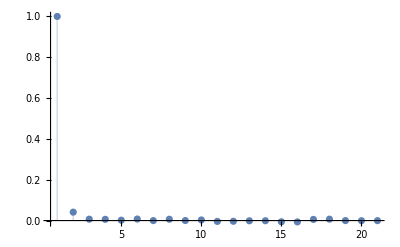

1.06246

```mathematica
(* LSB correlations *)
l2=Map[Mod[#,2]&,l];
Mean[l2]
cf=CorrelationFunction[l2,{20}]
ListPlot[cf,Filling->0,PlotRange->All]
Total[cf]
```